### Sensitivity of PSI-nEDM to long range spin-spin forces Author: Prajwal T Mohanmurthy (prajwal@mohanmurthy.com) From paper: PRL 103, 261801 (2009)

Setting Constants and Equations

{2.39399×10^6}

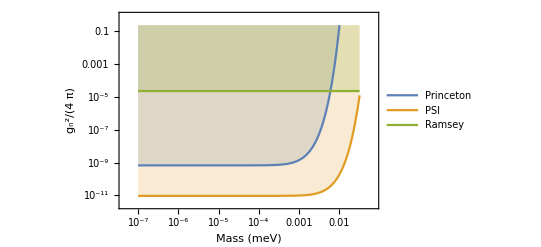

```mathematica
mn=.05(*in GeV*);
rexpp=.5 1/(.198×10^-6)(*Princeton: .5 m, expressed in natural units of GeV^-1*);
rexpn=.12 1/(.198×10^-6)(*PSI: .12 m, expressed in natural units of GeV^-1*);
bnyp=.56×10^-18×1/(.87)(*in T*);
bnyn=2×10^-12×1/10^4;
vexp[bny_]=((9.6623647×10^-27)/(1.6×10^-19))×bny(*v=\mu_n b^n_y*);
gp2b4p[m_,v_,r_] =(-4 v mn^2 ⅇ^(m r))/((m/r^2+1/r^3)-3(m^2/r+(3m)/r^2+3/r^3));
rtest=rr/.Solve[gp2b4p[0,vexp[bnyp],rr]==5.8×10^-10,rr,Reals];
rtest
lineStyle2={Thin,Blue,Dashed};
line21=Line[{{10^-7,2.3×10^-5},{10^-2,2.3×10^-5}}];
LogLogPlot[{ConditionalExpression[gp2b4p[mm/10^3,vexp[bnyp],rexpp],10^-7<mm<10^-2],gp2b4p[mm/10^3,vexp[bnyn],rexpn],2.3×10^-5},{mm,10^-7,10^-1.5},Frame->True,PlotRange->Full,PlotLegends->{"Princeton","PSI","Ramsey"},Filling->{1->Top,2->Top,3->Top},FrameLabel->{"Mass (meV)","g_n^2/(4  π)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},FrameTicks->{Table[{10^k,Superscript[10,k]},{k,-7,-2}],Table[{10^k,Superscript[10,k]},{k,-11,-1,2}]}]
```

```mathematica
rsol=
```

{0.195399}

```mathematica
(10^(-12)/rtest+(3 10^(-6))/rtest^2+3/rtest^3)/(10^(-6)/rtest^2+1/rtest^3)
```

{3.}

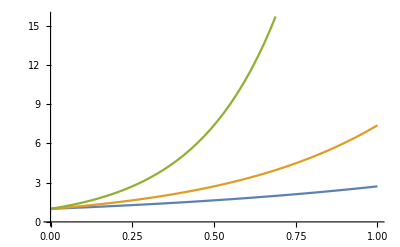

```mathematica
Plot[{Exp[x],Exp[2x],Exp[4x]},{x,0,1}]
```

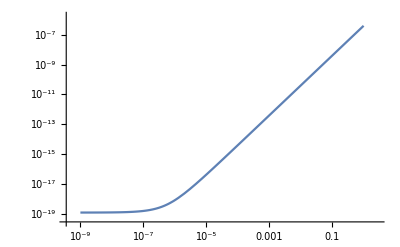

```mathematica
LogLogPlot[N[-(m/rexpmax^2+1/rexpmax^3)+(m^2/rexpmax+(3m)/rexpmax^2+3/rexpmax^3)],{m,10^(-9),10^(0)},PlotRange->Full]
```

### For Dark Photons

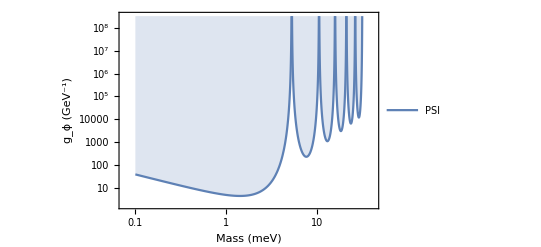

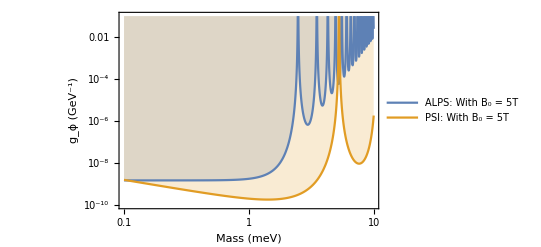

```mathematica
(*LASER*)
noh=24*200;
N[pmin=1/(noh×3600×10^9)];
lambda=10^-13;
w=(6.6×10^-34×3×10^8)/(1.6×10^-19)×1/lambda;
b=5;
l=5;
g[ma_]=(1.5×10^-15×(b^2 w^2)/(pmin ma^4)×Sin[1.267×(ma^2 l)/w]^2)^-2;
(*PSI*)
rho0=.43(*GeV cm^-3*);
rad=47/2;
hei=12;
vol=π rad^2 hei(*cm^3*);
b0=10^-6;
bmin=2 10^-12;
g2[ma_]=(1.5×10^-5 ×.43 vol √(2 ma)(1.5×10^-15 b0^2/(ma^2 bmin)Sin[1.267×10^4×ma(2 rad)]^2))^-2;
LogLogPlot[10^-14 g2[10^-6 mm],{mm,10^-1,10^1.5},Frame->True,PlotLegends->{"PSI"},Filling->{1->Top},FrameLabel->{"Mass (meV)","g_ϕ (GeV^-1)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},FrameTicks->{Automatic,Automatic},FrameLabel->"With B = 1μT"]
(*PLOT BOTH*)
LogLogPlot[{g[10^3 mm],.4 10^-24 g2[10^-6 mm]},{mm,10^-1,10^1},PlotRange->{{10^-1,10^1},{10^-10,10^-1}},Frame->True,Filling->{1->Top,2->Top},FrameLabel->{"Mass (meV)","g_ϕ (GeV^-1)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},FrameTicks->{Automatic,Automatic},PlotLegends->{"ALPS: With B_0 = 5T","PSI: With B_0 = 5T"}]
```